```mathematica
ClearAll["Global`*"];
```

```mathematica
dim = 60;
```

```mathematica
wp = 35;
```

```mathematica
$MaxExtraPrecision = 2000;
```

```mathematica
a = N[SparseArray[Band[{1, 2}] -> Sqrt[Range[dim - 1]], {dim, dim}], wp];
```

```mathematica
adag = ConjugateTranspose[a];
```

```mathematica
coherentState[(alpha_)?NumericQ] := coherentState[alpha] = Module[{z = N[alpha, wp], v},
   v = Table[Exp[-Abs[z]^2/2]*(z^n/Sqrt[n!]), {n, 0, dim - 1}];
   Normalize[v]];
```

```mathematica
catState[(r_)?NumericQ, (phi_)?NumericQ, (varphi_)?NumericQ] := catState[r,
   phi,
   varphi] = Module[{alpha = N[r*Exp[I*phi], wp]},
   Normalize[coherentState[alpha] + Exp[I*N[varphi, wp]]*coherentState[-alpha]]];
```

```mathematica
mpacs[(m_Integer)?NonNegative, (r_)?NumericQ, (phi_)?NumericQ, (varphi_)?NumericQ] := mpacs[m,
   r,
   phi,
   varphi] = Normalize[Nest[adag . #1 & , catState[r, phi, varphi], m]];
```

```mathematica
displacementMatrix[(beta_)?NumericQ] := displacementMatrix[beta] = Module[{b = N[beta, wp]},
   MatrixExp[b*adag - Conjugate[b]*a]];
```

```mathematica
psucc[(m_Integer)?NonNegative, (r_)?NumericQ, (phi_)?NumericQ, (varphi_)?NumericQ, (s_)?NumericQ, (delta1_)?NumericQ, (delta2_)?NumericQ] := Module[{psi, dp, dm, cH, cV, post},
   psi = mpacs[m, r, phi, varphi];
   dp = displacementMatrix[s/2] . psi;
   dm = displacementMatrix[-s/2] . psi;
   cH = Cos[N[delta2, wp]/2];
   cV = Exp[I*N[delta1, wp]]*Sin[N[delta2, wp]/2];
   post = ((cH + cV)*dp + (cH - cV)*dm)/2;
   N[Chop[Re[Conjugate[post] . post], 10^(-25)], 16]];
```

```mathematica
{r0, phi0, varphi0, s0, delta10, delta20, m0} = {1, Pi/2, Pi/2, 1/2, Pi/2, 8*(Pi/9), 1};
```

```mathematica
ss = {0, 3/10, 1/2, 7/10, 1};
```

```mathematica
rs = {1/2, 1, 2, 3, 4};
```

```mathematica
d2s = {1, 3, 5, 7, 8}*(Pi/9);
```

```mathematica
ms = Range[0, 4];
```

```mathematica
dataA = Table[Table[{delta2, psucc[m0, r0, phi0, varphi0, s, delta10, delta2]}, {delta2, Pi/40, 17*(Pi/18), Pi/40}],
   {s, ss}];
```

```mathematica
dataB = Table[Table[{phi, psucc[m0, r, phi, varphi0, s0, delta10, delta20]}, {phi, 0, 2*Pi, Pi/20}],
   {r, rs}];
```

```mathematica
dataC = Table[Table[{m, psucc[m, r0, phi0, varphi0, s0, delta10, delta2]}, {m, ms}],
   {delta2, d2s}];
```

```mathematica
font = "Times New Roman"; pw = 86/25.4*72 - 47; ph = 1.5 (.64 pw + 45) - 45; colors = {RGBColor[1,.24,.24],
  RGBColor[.16,.24,1],
  RGBColor[0,.68,.18],
  RGBColor[1,.5,0],
  RGBColor[.7,0,.74]};
```

```mathematica
styles = MapThread[Directive[#1,AbsoluteThickness[1.35],AbsoluteDashing[#2]]&,
   {colors,{{4,2},{1,1.8},{4,2},{4,1.8,1,1.8},{5,2}}}];
```

```mathematica
mark[i_] := Graphics[{EdgeForm[Directive[colors[[i]],AbsoluteThickness[.9]]],FaceForm[White],Switch[i,1,Disk[],2,Polygon[{{0,1},{-.866,-.5},{.866,-.5}}],3,Polygon[{{0,1},{1,0},{0,-1},{-1,0}}],4,Rectangle[{-1,-1},{1,1}],5,Polygon[{{0,-1},{-.866,.5},{.866,.5}}]]},
  PlotRange->{{-1.2,1.2},{-1.2,1.2}},
  ImagePadding->0,
  ImageSize->4,
  AspectRatio->1];
```

```mathematica
piLabel[n_,d_] := If[n==0,"0",Row[{If[n==1,"",n],"π/",d}]];
```

```mathematica
blank[t_] := {#[[1]],
  "",
  #[[3]]}& /@ t; ticks[major_,
  minor_] := Join[{#[[1]],#[[2]],{.017,0}}& /@ major,
  {#,"",{.009,0}}& /@ Select[minor,Min[Abs[#-major[[All,1]]]]>10^-7&]];
```

```mathematica
xt = {ticks[Table[{n Pi/9,piLabel[n,9]},{n,0,8,2}],Range[0,17] Pi/18],
  ticks[{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3 Pi/2,"3π/2"},{2 Pi,"2π"}},Range[0,40] Pi/20],
  ticks[Table[{n,n},{n,0,4}],Range[0,20]/5]};
```

```mathematica
yt = Table[{n/20,If[Mod[n,4]==0 && n<=20,NumberForm[N[n/20],{2,1},NumberPadding->{"","0"}],""],{If[Mod[n,4]==0,.017,.009],0}},
  {n,0,23}];
```

```mathematica
labels = {(Row[{Style["s",Italic]," = ",#}]& /@ {"0.0","0.3","0.5","0.7","1.0"}),
  (Row[{Style["r",Italic]," = ",#}]& /@ {"0.5","1","2","3","4"}),
  (Row[{Subscript[Style["δ",Italic],2]," = ",piLabel[#,9]}]& /@ {1,3,5,7,8})};
```

```mathematica
legend[i_] := Grid[Flatten /@ Partition[Table[{Graphics[{styles[[k]],Line[{{0,.5},{1,.5}}],Inset[mark[k],{.5,.5},Center,Offset[{4,4}]]},PlotRange->{{0,1},{0,1}},ImagePadding->0,ImageSize->{If[i==2,12,19],7}],labels[[i,k]]},{k,5}],If[i==2,3,2],If[i==2,3,2],1,{}],
  Alignment->{Left,Center},
  Spacings->{.4,.06},
  BaseStyle->{FontFamily->font,FontSize->10.5,Black}];
```

```mathematica
plot[data_,i_] := ListLinePlot[data,
  PlotStyle->styles,
  Axes->False,
  Frame->True,
  FrameLabel->{ {Subscript["δ",2],"φ",Style["m",Italic]}[[i]],If[i==1,Subscript[Style["P",Italic],"s"],None]},
  FrameTicks->{{If[i==1,yt,blank[yt]],blank[yt]},{xt[[i]],blank[xt[[i]]]}},
  FrameStyle->Directive[Black,AbsoluteThickness[1.25]],
  FrameTicksStyle->Directive[Black,AbsoluteThickness[.9],FontSize->11,FontFamily->font,FontWeight->Bold],
  LabelStyle->{FontFamily->font,FontSize->14,Black,ScriptSizeMultipliers->.85},
  BaseStyle->{FontFamily->font,FontSize->11},
  PlotRange->{{{0,17 Pi/18},{0,2 Pi},{-.05,4.05}}[[i]],{0,1.2}},
  PlotRangePadding->None,
  ImagePadding->{{If[i==1,44,6],If[i==3,10,6]},{42,3}},
  ImageSize->{pw+If[i==1,44,6]+If[i==3,10,6],ph+45},
  AspectRatio->ph/pw,
  Background->White,
  PlotRangeClipping->False,
  Epilog->Join[Flatten[Table[Inset[mark[k],#,Center,Offset[{4,4}]]& /@ data[[k,DeleteDuplicates[Append[Range[1,Length[data[[k]]],If[i==3,1,3]],Length[data[[k]]]]]]],{k,5}],1],{Inset[Style["("<>FromCharacterCode[96+i]<>")",FontFamily->font,FontSize->25,FontWeight->Bold,Black],Offset[{27,-1},Scaled[{0,1}]],{Left,Top}],Inset[legend[i],Scaled[{.98,.98}],{Right,Top}]}]];
```

```mathematica
figAll = With[{panels=MapIndexed[plot[#1,First[#2]]&,{dataA,dataB,dataC}],widths=pw+{50,12,16},h=ph+45},
  Graphics[Table[Inset[panels[[i]],{Total[Take[widths,i-1]],h},{Left,Top},{widths[[i]],h}],{i,3}],PlotRange->{{0,Total[widths]},{0,h}},ImagePadding->0,PlotRangePadding->None,ImageSize->{Total[widths],h},AspectRatio->h/Total[widths],Background->White]];
(* Enlarge display only; preserve all calculations and data. *)
figAll = Module[{grow, scale = 1.5, enlarged},
  grow[gr_Graphics] := Module[{primitives = First[gr], opts = Rest[List @@ gr]},
    Graphics[
      primitives /. Inset[p_Graphics, pos_, anchor_, size_List] :>
        Inset[grow[p], scale pos, anchor, scale size],
      Sequence @@ (opts /. {
        HoldPattern[ImageSize -> sz_List] :> (ImageSize -> scale sz),
        HoldPattern[ImagePadding -> pad_List] :> (ImagePadding -> scale pad),
        HoldPattern[PlotRange -> pr_List] /; MatchQ[primitives, {_Inset ..}] :>
          (PlotRange -> scale pr)
      })
    ]
  ];
  enlarged = grow[figAll];
  enlarged /. {
    HoldPattern[FontSize -> v_?NumericQ] :>
      (FontSize -> Switch[v, 10.5, 18, 11, 18, 14, 24, 21, 32, 25, 34, _, v]),
    AbsoluteThickness[1.35] -> AbsoluteThickness[2.7],
    AbsoluteThickness[1.25] -> AbsoluteThickness[1.6],
    AbsoluteThickness[.9] -> AbsoluteThickness[1.2],
    Offset[v_List] :> Offset[1.5 v],
    Offset[v_List, p_] :> Offset[1.5 v, p]
  }
];
figAll = Module[{items = First[figAll], options = Rest[List @@ figAll], panel, ticks, range, size, padding, panelSize, gap = 0},
  items = MapIndexed[Function[{item, index},
    panel = item[[1]] /. Grid[rows_, opts___] :>
      Grid[rows, Sequence @@ DeleteCases[{opts}, HoldPattern[Alignment -> _]], Alignment -> Left];
    If[True,
      ticks = FrameTicks /. Options[panel, FrameTicks];
      ticks[[1, 1]] = Map[Function[tick,
        If[tick[[2]] === "", tick,
          ReplacePart[tick, 2 -> (ToString[Quotient[Round[10 tick[[1]]], 10]] <> "." <> ToString[Mod[Round[10 tick[[1]]], 10]])]
        ]], ticks[[1, 1]]];
      padding = ImagePadding /. Options[panel, ImagePadding];
      panelSize = ImageSize /. Options[panel, ImageSize];
      panel = Show[panel, FrameTicks -> ticks, ImageSize -> panelSize + {12, 0},
        AspectRatio -> (panelSize[[2]] - Total[padding[[2]]])/(panelSize[[1]] - Total[padding[[1]]] + 12)];
      panel = panel /. Inset[Style[label_String, style___], Offset[{dx_, dy_}, anchor_], align_] /;
          MemberQ[{"(a)", "(b)", "(c)"}, label] :>
        Inset[Style[label, style], Offset[{dx + 6, dy}, anchor], align];
    ];
    ReplacePart[item, {1 -> panel,
      2 -> (item[[2]] + If[True, {12 (First[index] - 1), 0}, If[MemberQ[{3, 6}, First[index]], {gap, 0}, {0, 0}]]),
      4 -> (item[[4]] + If[True, {12, 0}, {0, 0}])}]
  ], items];
  range = PlotRange /. Options[figAll, PlotRange];
  size = ImageSize /. Options[figAll, ImageSize];
  range[[1, 2]] += If[True, 36, gap]; size[[1]] += If[True, 36, gap];
  Graphics[items, Sequence @@ DeleteCases[options, HoldPattern[(PlotRange | ImageSize | AspectRatio) -> _]],
    PlotRange -> range, ImageSize -> size, AspectRatio -> size[[2]]/size[[1]]]
];
figAll = Magnify[figAll, 1.5];
figAll = figAll /. {
  legend_Grid :> (legend /. HoldPattern[FontSize -> v_?NumericQ] :> (FontSize -> 1.2 v)),
  HoldPattern[Inset[Style[tag_String, style___], Offset[{dx_, dy_}, _Scaled], align_]] /; StringMatchQ[tag, "(" ~~ LetterCharacter ~~ ")"] :>
    Inset[Style[tag, Sequence @@ ({style} /. HoldPattern[FontSize -> v_?NumericQ] :> (FontSize -> 1.2 v))], Offset[{10, dy}, Scaled[{0, 1}]], align]
};
```

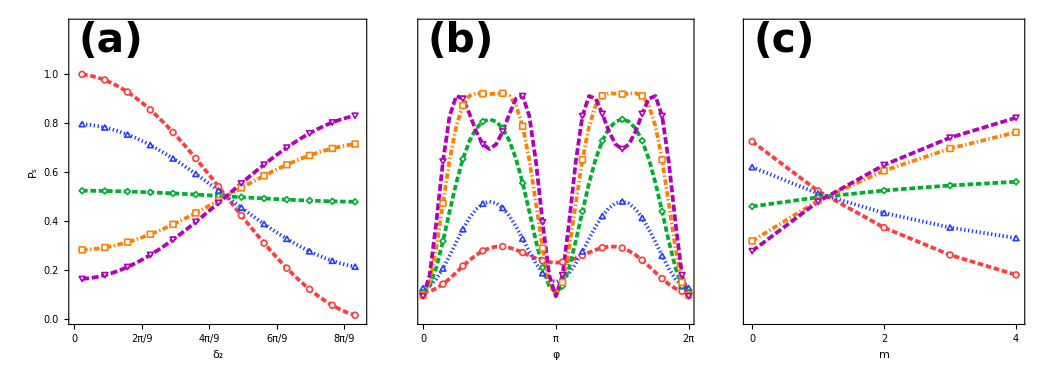

```mathematica
figAll
```

```mathematica
img = Rasterize[figAll, "Image", RasterSize -> {4145, Automatic}, Background -> White];
Export[FileNameJoin[{NotebookDirectory[], "Fig.2.png"}], img, "PNG"];
```